```mathematica
file="/Users/vpk/Google\ Drive/Jlab/Projects/Mathematica/densities.txt";
Hdata=ReadList[file,{Number,Number,Number,Number,Number}];
X=Hdata[[All,1]];

HForwardu=Hdata[[All,2]];
HProfileu=Hdata[[All,3]];
HForwardd=Hdata[[All,4]];
HProfiled=Hdata[[All,5]];

xmin=1.9924×10^-5;
xmax=0.5;
ymin=0;
ymax=15;
HFu=Interpolation[Thread[{X,HForwardu}],InterpolationOrder->1];
HFd=Interpolation[Thread[{X,HForwardd}],InterpolationOrder->1];
HPu=Interpolation[Thread[{X,HProfileu}],InterpolationOrder->1];
HPd=Interpolation[Thread[{X,HProfiled}],InterpolationOrder->1];
Hu[x_,t_]:=HFu[x]*Exp[HPu[x]*t];
Hd[x_,t_]:=HFd[x]*Exp[HPd[x]*t];

PlotFL=Plot[{HFu[x],HFd[x]},{x,xmin,xmax},PlotRange->{{xmin,xmax},{ymin,ymax}},FrameLabel->{"x","Forward Limit"},PlotLegends->Placed[{u-quark,d-quark},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel->"Forward Limit"];
PlotPF=Plot[{HPu[x],HPd[x]},{x,xmin,xmax},PlotRange->{{xmin,xmax},{ymin,ymax}},FrameLabel->{"x","Profile FUnction"},PlotLegends->Placed[{u-quark,d-quark},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel->"Profile Function"];
xx=0.1;
 PlotH=Plot[{Hu[0.1,-t],Hd[0.1,-t]},{t,0,1},FrameLabel->{"-t","H(x=0.1,-t"},PlotLegends->Placed[{u-quark,d-quark},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel-> "H(x=0.1,-t)"];
PlotHu=DensityPlot[Hu[x,-t],{x,0.1,0.5},{t,0,1},ColorFunction->"SunsetColors",PlotLegends->Automatic];
PlotHd=DensityPlot[Hd[x,-t],{x,0.1,0.5},{t,0,1},ColorFunction->"SunsetColors",PlotLegends->Automatic];

(* Peter*)
Au=0.5; nu=4.83; Bu=0.5; αu=0.3; αu'=0.45;
Ad=0.5; nd=3.57; Bd=0.5; αd=0.3; αd'=0.45;
(*Fit*)
Au=0.5; nu=16.7; Bu=0.71;   αu=-0.058; αu'=0.38;  βu=4;
Ad=0.5; nd= 4.2;  Bd=-1.22; αd=0.42;     αd'=1.79;  βd=5;

(*Fit with COMPASS*)
Au=0.5; nu=21.99; Bu=1.0812;   αu=-0.15798;  αu'=0.23607;  βu=4;
Ad=0.5; nd=  9.29;  Bd=-0.00178;  αd=  0.165;     αd'=1.44;     βd=5;


(*ETPFu[x_]:=(Bu+αu'Log[1./x])*(1.-x)^3+Au*x*(1.-x)^2;*)
ETPFu[x_]:=(Bu+αu'Log[1./x]);
ETFLu[x_]:=nu*x^(-αu)*(1.-x)^βu;

(*ETPFd[x_]:=(Bd+αd'Log[1./x])*(1.-x)^3+Ad*x*(1.-x)^2;*)
ETPFd[x_]:=(Bd+αd'Log[1./x]);
ETFLd[x_]:=nd*x^(-αd)*(1.-x)^βd;

ETu[x_,t_]:=ETFLu[x]*Exp[ETPFu[x]*t];
ETd[x_,t_]:=ETFLd[x]*Exp[ETPFd[x]*t];

GeVFm=0.1973;

HDeNu  [x_,bx_,by_]:=1./(4*π)*HFu[x]/HPu[x]*Exp[-(bx^2+by^2)/(4*HPu[x])];
ETDeNu[x_,bx_,by_]:=1./(4*π)*ETFLu[x]/ETPFu[x]*Exp[-(bx^2+by^2)/(4*ETPFu[x])];
DeNETu [x_,bx_,by_]:=1./2.*(0+1./4.*by/(0.938*ETFLu[x])*ETDeNu[x,bx,by]);
DeNu     [x_,bx_,by_]:=1./2.*(HDeNu[x,bx,by]+1./4.*by/(0.938*ETFLu[x])*ETDeNu[x,bx,by]);
DenXYu[x_,bx_,by_]:=DeNu[x,bx/GeVFm,by/GeVFm]*GeVFm^2;

HDeNd  [x_,bx_,by_]:=1./(4*π)*HFd[x]/HPd[x]*Exp[-(bx^2+by^2)/(4*HPd[x])];
ETDeNd[x_,bx_,by_]:=1./(4*π)*ETFLd[x]/ETPFd[x]*Exp[-(bx^2+by^2)/(4*ETPFd[x])];
DeNETd [x_,bx_,by_]:=1./2.*(0+1./4.*by/(0.938*ETFLd[x])*ETDeNd[x,bx,by]);DeNd     [x_,bx_,by_]:=1./2.*(HDeNd[x,bx,by]+1./4.*by/(0.938*ETFLd[x])*ETDeNd[x,bx,by]);
DenXYd[x_,bx_,by_]:=DeNd[x,bx/GeVFm,by/GeVFm]*GeVFm^2;



xd=0.42;
(*Print["HFu",[xx],"=",HFu[xd]]
Print["HPu",[xd],"=",HPu[xd]]
Print["HDeNu[0.,0.]=",HDeNu[xd,0.,0.]]
Print["DenXYu[0.,0.]=",DenXYu[xd,0.,0.]]
Print["DenXYd[0.,0.]=",DenXYd[xd,0.,0.]]*)
```

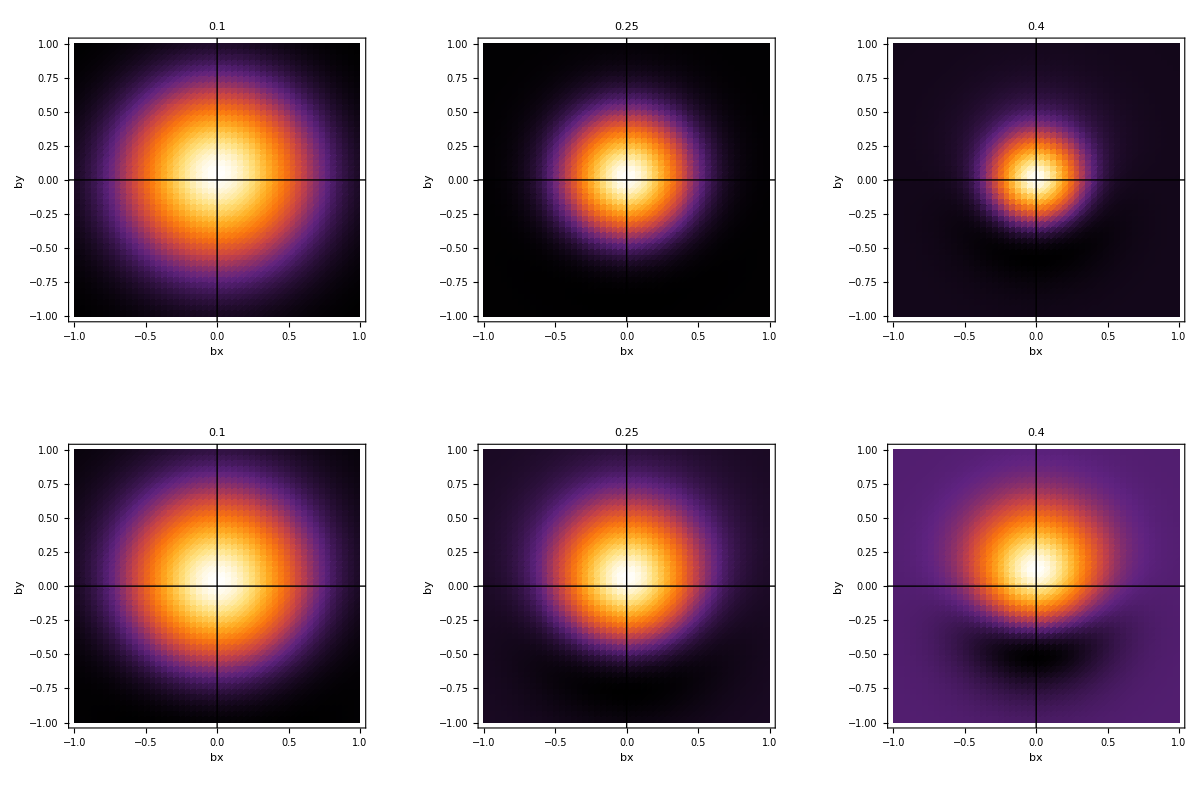

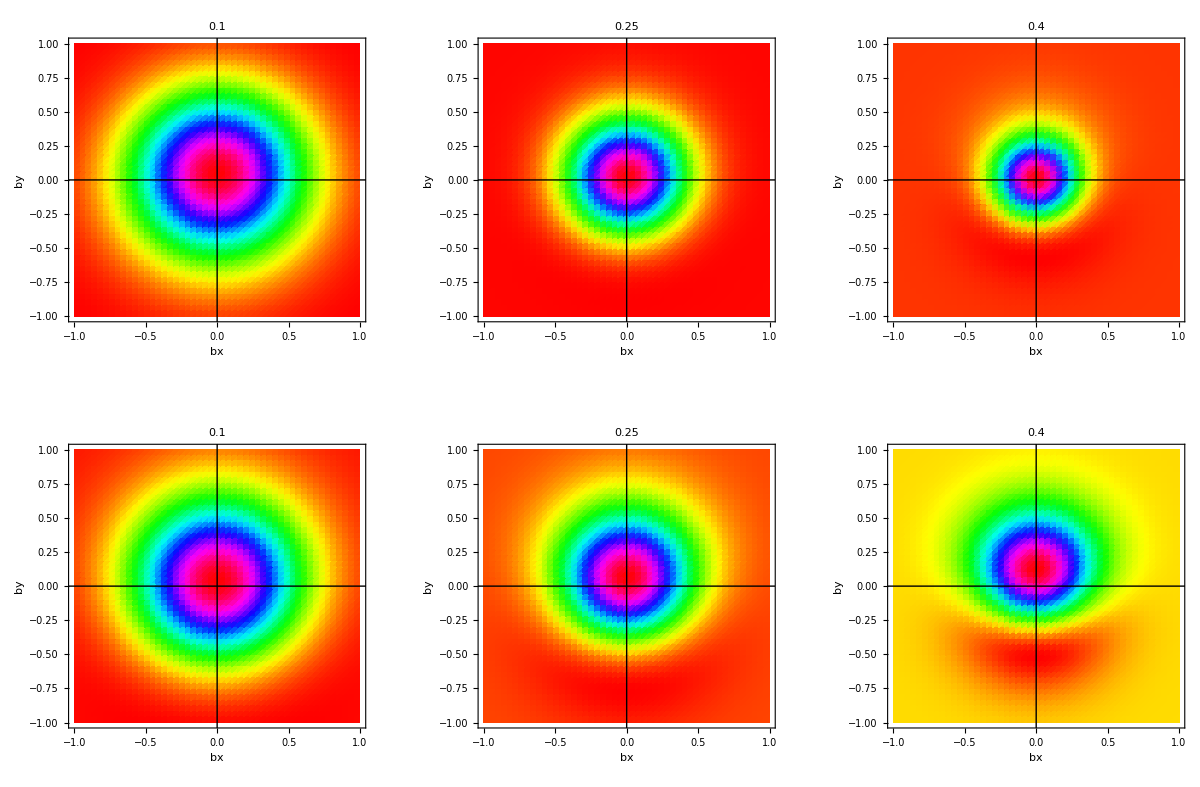

```mathematica
plotGPDu[xz_,colfun_]:=DensityPlot[DenXYu[xz,bx,by],{bx,-1,1},{by,-1,1},
PlotLabel->Style[StandardForm[xz],FontSize->25,FontColor->Black],
PlotLegends->BarLegend[None],
ColorFunction->colfun,
PlotPoints->50,
PlotRange->All,Axes->True,AxesLabel->{bx,by},
ImageSize->Automatic,
PlotLegends->None,
Epilog->{Directive[{Thin,Black}],Line[{{-5,0},{5,0}}],Line[{{0,-5},{0,5}}]}];
plotGPDd[xz_,colfun_]:=DensityPlot[DenXYd[xz,bx,by],{bx,-1,1},{by,-1,1},
PlotLabel->Style[StandardForm[xz],FontSize->25,FontColor->Black],
PlotLegends->BarLegend[None],
ColorFunction->colfun,
PlotPoints->50,
PlotRange->All,Axes->True,AxesLabel->{bx,by},
ImageSize->Automatic,
Epilog->{Directive[{Thin,Black}],Line[{{-5,0},{5,0}}],Line[{{0,-5},{0,5}}]}];

colfun3="Rainbow";
colfun1="SunsetColors";
colfun2=Hue;


p10u1=plotGPDu[0.10,colfun1];
p25u1=plotGPDu[0.25,colfun1];
p35u1=plotGPDu[0.40,colfun1];
p10d1=plotGPDd[0.10,colfun1];
p25d1=plotGPDd[0.25,colfun1];
p35d1=plotGPDd[0.40,colfun1]; 
GraphicsGrid[{{p10u1,p25u1,p35u1},{p10d1,p25d1,p35d1}},ImageSize->Full]

p10u2=plotGPDu[0.10,colfun2];
p25u2=plotGPDu[0.25,colfun2];
p35u2=plotGPDu[0.40,colfun2];
p10d2=plotGPDd[0.10,colfun2];
p25d2=plotGPDd[0.25,colfun2];
p35d2=plotGPDd[0.40,colfun2]; 
GraphicsGrid[{{p10u2,p25u2,p35u2},{p10d2,p25d2,p35d2}},ImageSize->Full]

(*plotGPDu[0.10,colfun1]   plotGPDu[0.10,colfun2]
plotGPDu[0.25,colfun1]   plotGPDu[0.25,colfun2]
plotGPDu[0.35,colfun1]  plotGPDu[0.35,colfun2]
plotGPDd[0.10,colfun1]  plotGPDd[0.10,colfun2]
plotGPDd[0.25,colfun1]  plotGPDd[0.25,colfun2]
plotGPDd[0.35,colfun1]  plotGPDd[0.35,colfun2]*)
```

```mathematica
plotu=Plot3D[DenXYu[0.40,bx,by],{bx,-1,1},{by,-1,1},
PlotLabel->Style[StandardForm["u quark"],FontSize->25,FontColor->Black],
PlotLegends->BarLegend[None], 
ColorFunction->"Rainbow",
PlotPoints->50,
PlotRange->All,Axes->True,AxesLabel->{bx,by},
ImageSize->Large];
plotd=Plot3D[DenXYd[0.40,bx,by],{bx,-1,1},{by,-1,1},
PlotLabel->Style[StandardForm["d quark"],FontSize->25,FontColor->Black],
PlotLegends->BarLegend[None],
ColorFunction->"Rainbow",
PlotPoints->50,
PlotRange->All,Axes->True,AxesLabel->{bx,by},
ImageSize->Large];
GraphicsGrid[{{plotu,plotd}},ImageSize->Full]
```

-Graphics-

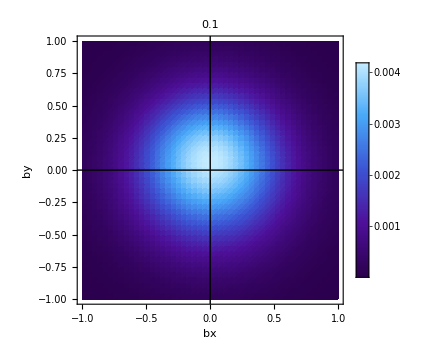
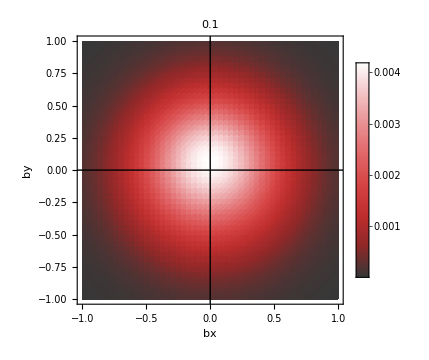
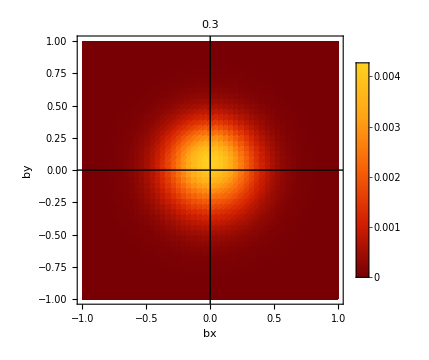
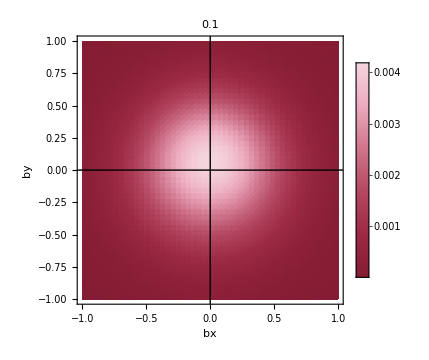

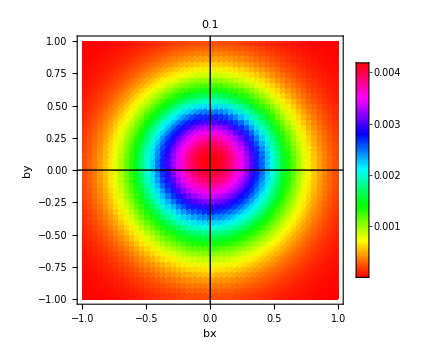
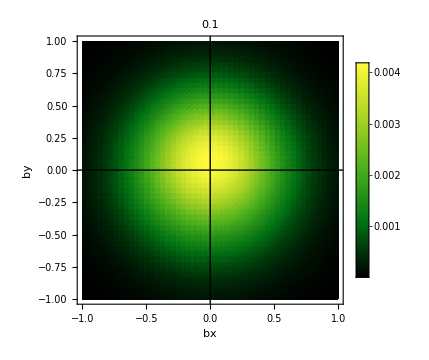
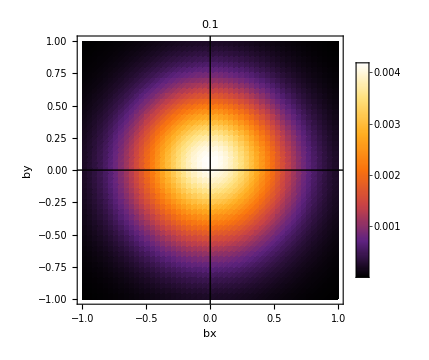
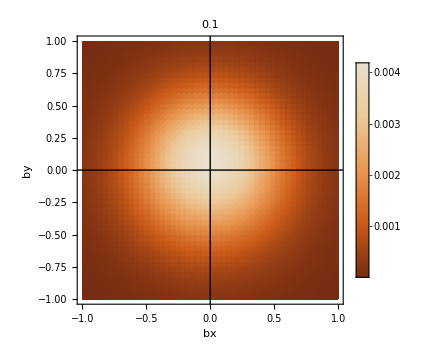

-Graphics- -Graphics- -Graphics- -Graphics-

```mathematica
plotGPDu[0.30,"SolarColors"]     plotGPDu[0.10,"DeepSeaColors"] plotGPDu[0.10,"CherryTones"]  plotGPDu[0.10,"ValentineTones"]

plotGPDu[0.1,"SunsetColors"]  plotGPDu[0.10,"SiennaTones"] plotGPDu[0.10,"AvocadoColors"] plotGPDu[0.10,Hue]

plotGPDu[0.1,"VisibleSpectrum"]  plotGPDu[0.10,"SiennaTones"] plotGPDu[0.10,"AvocadoColors"] plotGPDu[0.10,Hue]

{ColorSlider[Dynamic[x]],Dynamic[x]}
```

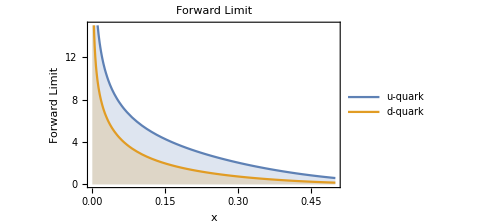

```mathematica
PlotFL
```

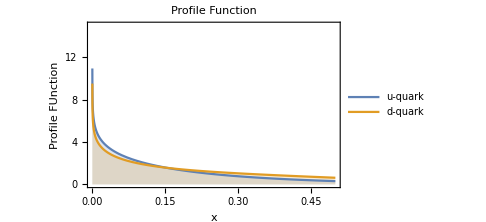

```mathematica
PlotPF
```

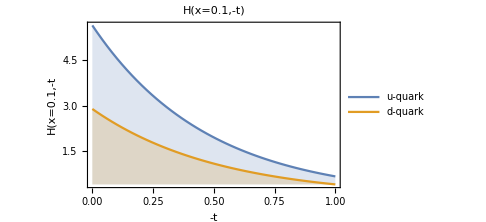

```mathematica
PlotH
```